```mathematica
Clear["Global`*"]
```

```mathematica
λ= (δ 16 N[π]^2)/19((20 + 6 √23)^(1/2) - √23- 1);
U [ϕ_]:= Simplify[(λ ϕ^4(ϕ/μ)^((-16 δ)/19))/(4 NF^2 (1 + (ξ ϕ^2)/M^2)^2)];
dphiU[ϕ_] :=FullSimplify[D[U[ϕ],ϕ]]

ddphiU[ϕ_]:= FullSimplify[D[dphiU,ϕ]]
```

```mathematica
M=22*10^-9;
NF= 10;
μ = 10^-3 M;
ξ =1/6
δ = .1;
```

1/6

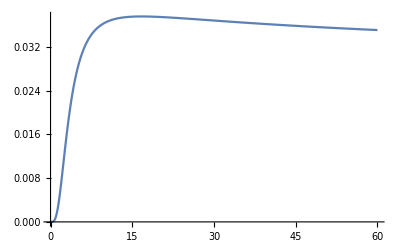

```mathematica
Plot[U[ϕ*M]/M^4,{ϕ,0,60},PlotRange->All]
```

```mathematica
v= U[ϕ*M]/(24 Pi^2 M^4 )
```

(0.000209706 ϕ^3.91579)/((6.+ϕ^2)^2)

Obliczamy prawdopodobieństwo tunelowania z lewej strony potencjału na prawo p_+ (ϕ_0)

```mathematica
denominator=SetPrecision[NIntegrate[SetPrecision[Exp[1/Subscript[v, max]] Exp[-1/v],1000],{ϕ,0,∞},AccuracyGoal->Infinity],100000000000]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
numerator=NIntegrate[Exp[-1/v],{ϕ,0,16.6}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
numerator/denominator
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Exp[1/Subscript[v, max]]
```

1.4508487622×10^11371

General::munfl: Exp[-6504.46] is too small to represent as a normalized machine number; precision may be lost.

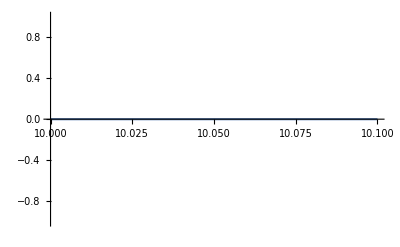

```mathematica
Plot[Exp[1/Subscript[v, max]]Exp[-1/v],{ϕ,10,10.1}]
```

```mathematica
Series[-1/v,{ϕ,16.7,3}]
```

-6307.3+0.0122803 (ϕ-16.7)-1.86546 (ϕ-16.7)^2+0.183019 (ϕ-16.7)^3+O[ϕ-16.7]^4

```mathematica
-6307.295520650616+0.012280288517012107 (ϕ-16.7)-1.8654586194535119 (ϕ-16.7)^2+0.18301898304534717 (ϕ-16.7)^3+O[ϕ-16.7]^4
```

-6307.3+0.0122803 (ϕ-16.7)-1.86546 (ϕ-16.7)^2+0.183019 (ϕ-16.7)^3+O[ϕ-16.7]^4

```mathematica
0.00015854655877878496+3.086897511732341*^-10 (ϕ-16.7)-4.689205379698341*^-8 (ϕ-16.7)^2+4.600367647611412*^-9 (ϕ-16.7)^3+O[ϕ-16.7]^4
```

0.000158547+3.0869×10^-10 (ϕ-16.7)-4.68921×10^-8 (ϕ-16.7)^2+4.60037×10^-9 (ϕ-16.7)^3+O[ϕ-16.7]^4

```mathematica
numerator=NIntegrate[SetPrecision[Exp[-6307.295520650616+0.012280288517012107 (ϕ-16.7)-1.8654586194535119 (ϕ-16.7)^2+0.18301898304534717 (ϕ-16.7)^3],100000],{ϕ,0,16.6}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
r=FindRoot[U'[Subscript[ϕ, max]]==0,{Subscript[ϕ, max],16*M}];
Subscript[v, max]=U[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
dv=U'[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
ddv=U''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
dddv=U'''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
```

```mathematica
R=1-2/3 √(2/Pi)(Subscript[v, max] dddv)/Abs[ddv]^(3/2)
```

0.918922

```mathematica
Rdenimonaator=√(Pi/2)(Subscript[v, max] Exp[-1/Subscript[v, max]])/(√Abs[ddv])(1+√(2/Pi)(Subscript[v, max] dddv)/(3 Abs[ddv]^(3/2)))
```

General::munfl: Exp[-6307.3] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Exp[-1/(0.03/(24 Pi^2))]
```

General::munfl: Exp[-7895.68] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
MaximaMatrix=Import["C:\\Users\\Janek\\Desktop\\AS\\Eternal inflation\\Sannino\\MaximalFieldValues.txt","Table"];
```

```mathematica
DeltaList=Import["C:\\Users\\Janek\\Desktop\\AS\\Eternal inflation\\Sannino\\Delta.txt","List"];
```

```mathematica
KsiList=Import["C:\\Users\\Janek\\Desktop\\AS\\Eternal inflation\\Sannino\\Ksi.txt","List"];
```

```mathematica
(*r={ξ->KsiList[[k]],δ->DeltaList[[d]],Subscript[ϕ, max]->MaximaMatrix[[d,k]]}
Subscript[v, max]=U[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r
dv=U'[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r
ddv=U''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r
dddv=U'''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r*)
```

```mathematica
M=Table[      
r={ξ->KsiList[[k]],δ->DeltaList[[d]],Subscript[ϕ, max]->MaximaMatrix[[d,k]]};
Subscript[v, max]=U[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
dv=U'[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
ddv=U''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;
dddv=U'''[Subscript[ϕ, max]]/(24 Pi^2 M^4 )/.r;      
1-2/3 √(2/Pi)(Subscript[v, max] dddv)/Abs[ddv]^(3/2)
 ,{d,Length[DeltaList]},{k,Length[KsiList]}];
```

```mathematica
formattedData=Flatten[#,1]&@Table[{DeltaList[[d]],KsiList[[k]],M[[d,k]]},{d,1,Length[DeltaList]},{k,1,Length[KsiList]}]
```

{{0.0001,0.1,1.02128},{0.0001,1.1,1.02128},{0.0001,2.1,1.02128},{0.0001,3.1,1.02128},{0.0001,4.1,1.02128},{0.0001,5.1,1.02128},{0.0001,6.1,1.02128},{0.0001,7.1,1.02128},9985,{0.0991,93.1,1.02566},{0.0991,94.1,1.02566},{0.0991,95.1,1.02567},{0.0991,96.1,1.02567},{0.0991,97.1,1.02568},{0.0991,98.1,1.02568},{0.0991,99.1,1.02569}}
 |  |  |  |

Poniżej wykres przedstawiający R = (p_+)/(p_-) na szczycie potencjału:

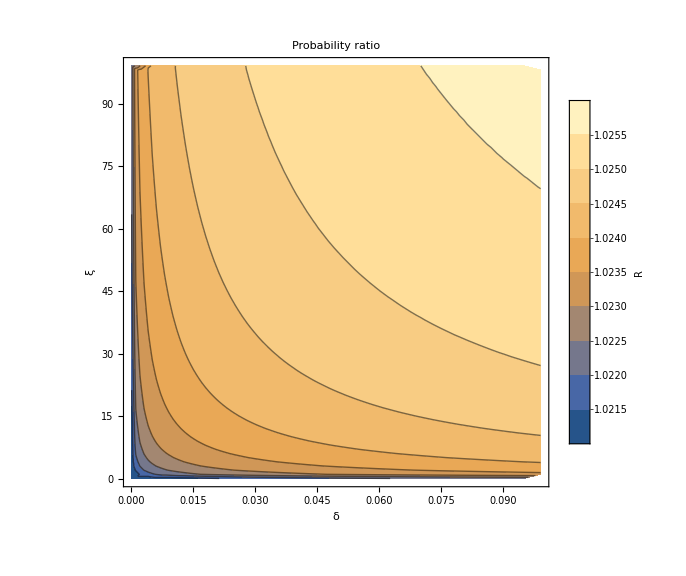

```mathematica
Rcontour=ListContourPlot[formattedData,FrameLabel->{Style["δ",FontSize->30],Style["ξ",FontSize->30]},TicksStyle->Directive["Label", 20], PlotTheme->"Default",FrameStyle->Directive[FontSize, 20],PlotLabel->Style["Probability ratio",FontSize->30],PlotLegends->{BarLegend[Automatic,LabelStyle->Directive[FontSize->20],LegendLabel->Placed[Style["R",FontSize->30, Gray],After]]},ImageSize->Large]
```

```mathematica
Export["Rcontour.jpg",Rcontour]
```

Rcontour.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rcontour.jpg"]]]
```

```mathematica
SystemOpen["rcontour.jpg"]
```

```mathematica
SystemOpen["rcontour.jpg"]
```

Robimy contour Plot ϕ_max jako funkcji (δ, ξ)

```mathematica
formattedData2=Flatten[#,1]&@Table[{DeltaList[[d]],KsiList[[k]],MaximaMatrix[[d,k]]},{d,1,Length[DeltaList]},{k,1,Length[KsiList]}]
```

{{0.0001,0.1,59.999},{0.0001,1.1,59.999},{0.0001,2.1,59.999},{0.0001,3.1,59.999},{0.0001,4.1,59.999},{0.0001,5.1,59.999},{0.0001,6.1,59.999},{0.0001,7.1,59.999},9985,{0.0991,93.1,0.71},{0.0991,94.1,0.706},{0.0991,95.1,0.702},{0.0991,96.1,0.699},{0.0991,97.1,0.695},{0.0991,98.1,0.692},{0.0991,99.1,0.688}}
 |  |  |  |

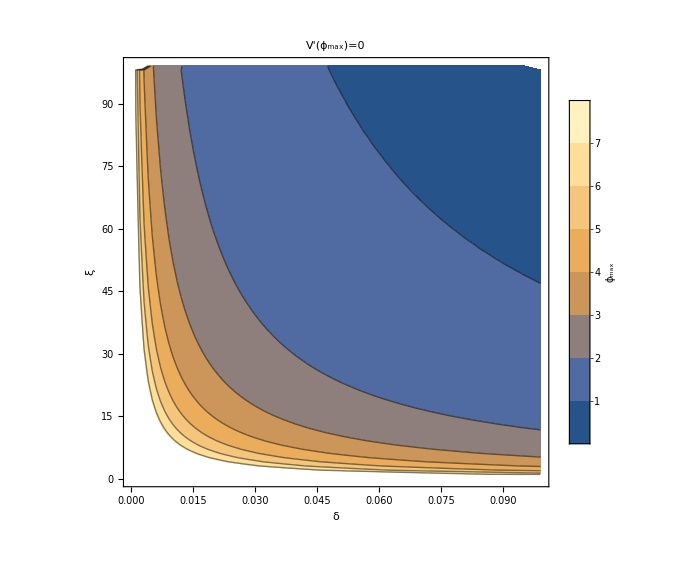

```mathematica
PhiMaxContour=ListContourPlot[formattedData2,FrameLabel->{Style["δ",FontSize->30],Style["ξ",FontSize->30]},TicksStyle->Directive["Label", 20], PlotTheme->"Default",FrameStyle->Directive[FontSize, 20],PlotLabel->Style["V'(ϕ_max)=0 ",FontSize->30],PlotLegends->{BarLegend[Automatic,LabelStyle->Directive[FontSize->20],LegendLabel->Placed[Style["ϕ_max",FontSize->30,Gray],After]]},ImageSize->Large]
```

```mathematica
Export["PhiMaxContour.jpg",PhiMaxContour]
```

PhiMaxContour.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PhiMaxContour.jpg"]]]
```

```mathematica
matrix={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
ArrayReshape[matrix,{9}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
RList=ArrayReshape[M,{Length[DeltaList]*Length[KsiList]}];
```

```mathematica
PhiMaxList=ArrayReshape[MaximaMatrix,{Length[DeltaList]*Length[KsiList]}];
```

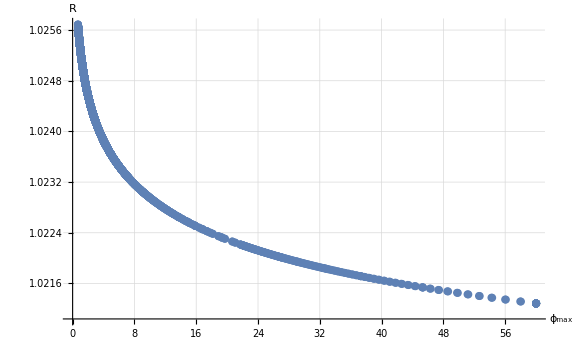

```mathematica
Data3=Transpose@{PhiMaxList,RList};
RPhiMaxPlot=ListPlot[Data3, PlotRange->All,GridLines->Automatic(*,PlotLabel->Style["R(ϕ_max)",FontSize->16]*),AxesLabel->{"ϕ_max","R"},AxesStyle->Directive[FontSize->16],ImageSize->Large,PlotStyle->PointSize[0.01]]
```

```mathematica
Export["Rphimax.jpg",RPhiMaxPlot]
```

Rphimax.jpg

```mathematica
RAwayList={0.968503937007874,0.89000189000189,0.898253606681853,0.867413632119514,0.832508704416346,0.822157434402332,0.817520901490367,0.80766449746927,0.772735330615139,0.58202816010125,0.440507058484587,0.323626737260093,0.223990208078335,1.02388180530257,1.29463056447912,1.70416441319632,2.2626427406199,3.1101520756268};
ϕAwayList={16.71,16.6,16.5,16.4,16.3,16.2,16.1,16,15.9,15,14,13,12,17,18,19,20,21};
Data4=Transpose@{ϕAwayList,RAwayList};
```

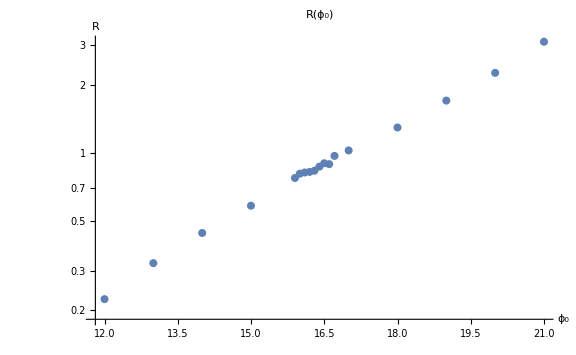

```mathematica
RPhiAwayPlot=ListLogPlot[Data4, PlotRange->All,GridLines->Automatic,PlotLabel->Style["R(ϕ_0)",FontSize->16],AxesLabel->{"ϕ_0","R"},AxesStyle->Directive[FontSize->16],ImageSize->Large,PlotStyle->PointSize[0.01]]
```

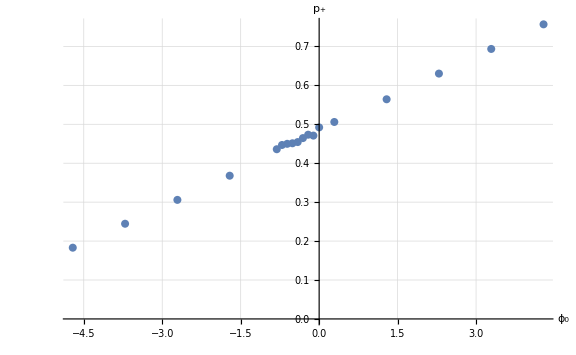

```mathematica
PprawoList={0.492,0.4709,0.4732,0.4645,0.4543,0.4512,0.4498,0.4468,0.4359,0.3679,0.3058,0.2445,0.183,0.5059,0.5642,0.6302,0.6935,0.7567};
P0minusPmaxList={0,-0.109999999999999,-0.210000000000001,-0.310000000000002,-0.41,-0.510000000000002,-0.609999999999999,-0.710000000000001,-0.810000000000001,-1.71,-2.71,-3.71,-4.71,0.289999999999999,1.29,2.29,3.29,4.29};
Data5=Transpose@{P0minusPmaxList,PprawoList};
PprawoAwayPlot=ListPlot[Data5, PlotRange->All,GridLines->Automatic,PlotLabel->Style["",FontSize->16],AxesLabel->{"ϕ_0","p_+"},AxesStyle->Directive[FontSize->16],ImageSize->Large,PlotStyle->PointSize[0.01]]
```

b+a x

{a→0.0640716,b→0.484175}

Function[{x},0.484175+0.0640716 x]

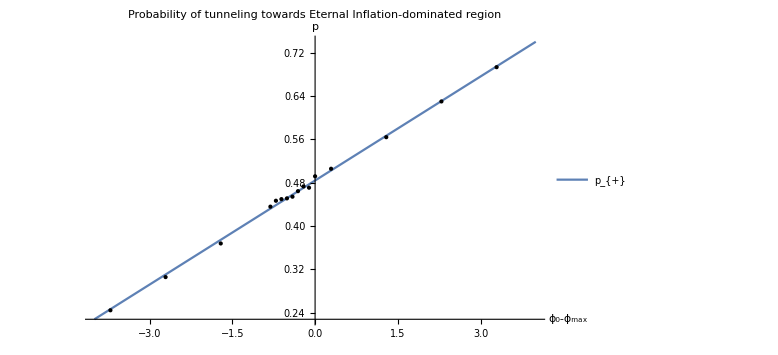

```mathematica
model=a*x+b
fit=FindFit[Data5,model,{a,b},x]
modelf=Function[{x},Evaluate[model/.fit]]
Plot[modelf[x],{x,-4,4},PlotRange->All,Epilog->Map[Point,Data5],PlotTheme->"Default",PlotLabel->Style["Probability of tunneling towards Eternal Inflation-dominated region",FontSize->17],ImageSize->Large,PlotTheme->"Classic",AxesLabel->{Style[Subscript[ϕ,0]-Subscript[ϕ,max],Large],Style["p",Large]},PlotLegends->{"p_{+}"}]
```

b1+a1 x

{a1→-0.0640716,b1→0.515825}

Function[{x},0.515825-0.0640716 x]

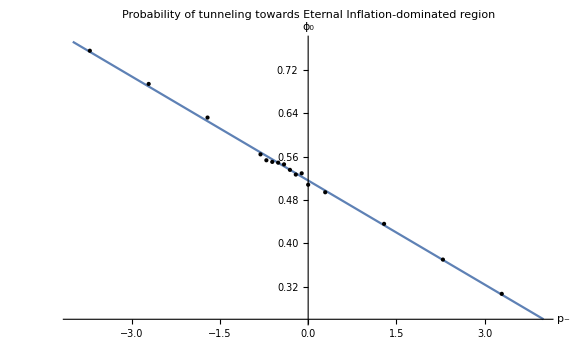

```mathematica
PlewoList={0.508,0.5291,0.5268,0.5355,0.5457,0.5488,0.5502,0.5532,0.5641,0.6321,0.6942,0.7555,0.817,0.4941,0.4358,0.3698,0.3065,0.2433};
Data6=Transpose@{P0minusPmaxList,PlewoList};
model1=a1*x+b1
fit1=FindFit[Data6,model1,{a1,b1},x]
modelf1=Function[{x},Evaluate[model1/.fit1]]
Plot[modelf1[x],{x,-4,4},PlotRange->All,Epilog->Map[Point,Data6],PlotTheme->"Default",PlotLabel->Style["Probability of tunneling towards Eternal Inflation-dominated region",FontSize->17],ImageSize->Large,PlotTheme->"Classic",AxesLabel->{Style["p_-",Large],Style[Subscript[ϕ,0],Large]}]
```

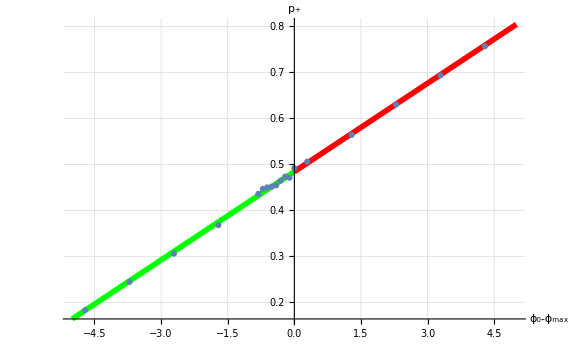

```mathematica
pplusplot=ListPlot[Data5,PlotMarkers->Automatic,PlotStyle->{DotDashed,Thick}(*,PlotLegends->{Style["p_+",FontSize->20]}*)];
pminusplot=ListPlot[Data6,PlotMarkers->Automatic,PlotStyle->{Dashed,Green},PlotLegends->{Style["p_-",FontSize->20]}];
pplusfit1=Plot[modelf[x],{x,-5,0},PlotStyle->{Green,Thickness->0.007}];
pminusfit1=Plot[modelf1[x],{x,-5,0},PlotStyle->Green];
pplusfit2=Plot[modelf[x],{x,0,5},PlotStyle->{Red,Thickness->0.007}];
pminusfit2=Plot[modelf1[x],{x,0,5},PlotStyle->Red];
S1=Show[pplusfit1,pplusfit2,pplusplot,GridLines->Automatic,PlotRange->All,(*PlotLabel->Style["Evolution probability towards Eeternal Inflaiton-dominated region",FontSize->16],*)AxesLabel->{"ϕ_0-ϕ_max","p_+"},AxesStyle->Directive[FontSize->16],ImageSize->Large,TicksStyle->Directive[FontSize->14]]
```

```mathematica
Export["TunnelingProbability.jpg",S1]
```

TunnelingProbability.jpg

```mathematica
FindRoot[modelf[x]==0,{x,-4}]
```

{x→-7.55678}

```mathematica
16.71-7.55677727811103
```

9.15322

```mathematica
FindRoot[modelf1[x]==0,{x,4}]
```

{x→8.05077}

```mathematica
16.71+8.050768459943455
```

24.7608